# Versuch 31

```mathematica
ClearAll["Global`*"]
```

## Plot Settings

```mathematica
pltsettings={Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->700,FrameTicksStyle->Directive[Black,15],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]};
```

```mathematica
ungewichteterReg[xdata_,ydata_]:=Module[{sx2=Total[xdata^2],sy=Total[ydata],sx=Total[xdata],sxy=Sum[xdata[[i]]ydata[[i]],{i,1,Length[xdata]}], n=Length[xdata],Δ,a,b,σ},Δ=(n sx2-sx^2);a=1/Δ(sx2 sy-sx sxy); b=1/Δ(n sxy-sx sy);σ=Sqrt[1/(n-2) Sum[(ydata[[i]]-a - b xdata[[i]])^2,{i,1,n}]];{a,b,σ Sqrt[sx2/Δ], σ Sqrt[n/Δ]}]
```

## Import Data

```mathematica
rawData=Import[NotebookDirectory[]<>"Entmagnetisierung.txt"];
```

```mathematica
data=Map[StringReplace["E"->"*10^"],Map[StringReplace[","->"."],StringSplit[StringSplit[rawData,"\n"],"	"]]][[2;;]];
```

```mathematica
data=Map[ToExpression,data,{2}];
```

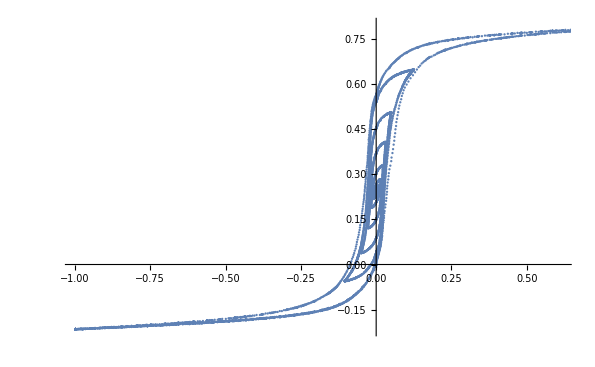

```mathematica
ListPlot[data[[All,{2,3}]]]
```

## Parameters

```mathematica
da=260*10^(-3);
di=220*10^(-3);
h=30*10^(-3);
```

```mathematica
N1=1010;
d=(da+di)/2;
R=0.2;
```

```mathematica
N2=53;
A=h (da-di)/2;
messbereich=100;
fullfaktor=1;
```

```mathematica
dataProcessed={N1 #[[1]]/(π d R),(messbereich/1000)((#1⟦2⟧)/(N2 fullfaktor A))}&/@data[[All,{2,3}]];
```

```mathematica
xpos = (Max[dataProcessed[[All,1]]]+Min[dataProcessed[[All,1]]])/2
ypos = (Max[dataProcessed[[All,2]]]+Min[dataProcessed[[All,2]]])/2
```

6.69777

0.915094

```mathematica
dataShifted={#[[1]]-xpos,#[[2]]-ypos}&/@dataProcessed;
```

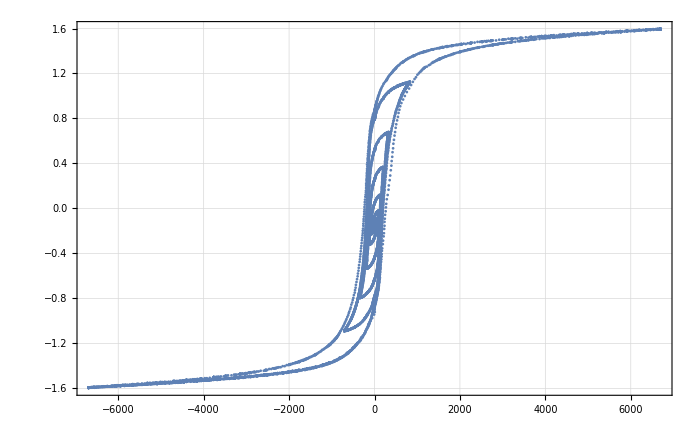

```mathematica
ListPlot[dataShifted,pltsettings,PlotRange->All]
```

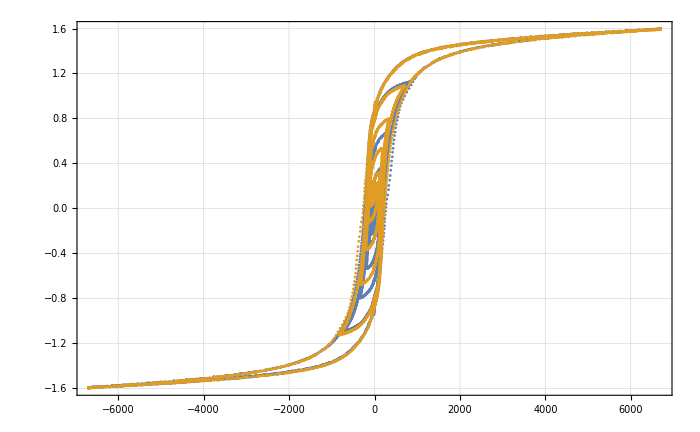

```mathematica
ListPlot[{dataShifted,-dataShifted},pltsettings,PlotRange->All]
```

## Export

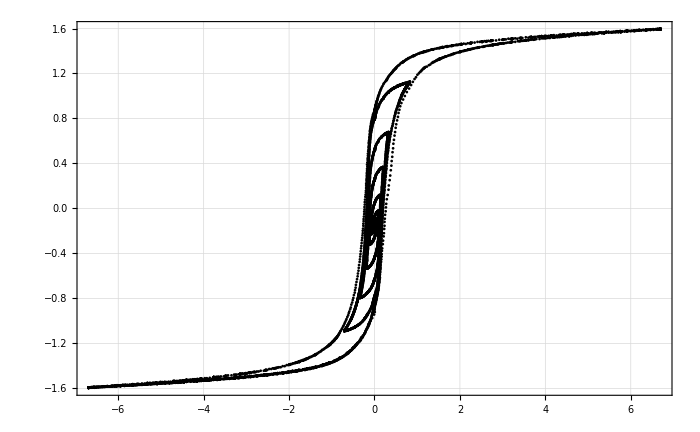

```mathematica
ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,pltsettings,PlotStyle->Black,PlotRange->All]
```

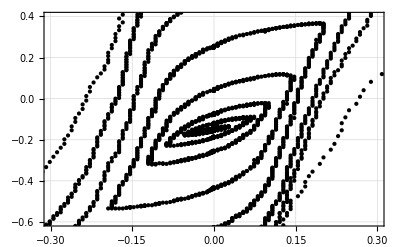

```mathematica
ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,PlotStyle->Directive[Black,PointSize[0.0075]],PlotRange->{{-0.3,0.3},{-0.6,0.4}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->400,FrameTicksStyle->Directive[Black,10],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]]
```

```mathematica
Export[NotebookDirectory[]<>"abbildungen/entmagnetisierung raw.pdf",ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,pltsettings,PlotStyle->Black,PlotRange->All],Background->None];
Export[NotebookDirectory[]<>"abbildungen/entmagnetisierung subplot raw.pdf",ListPlot[{#[[1]]/1000,#[[2]]}&/@dataShifted,PlotStyle->Directive[Black,PointSize[0.0075]],PlotRange->{{-0.3,0.3},{-0.6,0.4}},Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.003]],ImageSize->400,FrameTicksStyle->Directive[Black,10],GridLines->Automatic,GridLinesStyle->Directive[Gray,Thickness[0.002],Opacity[0.8]]],Background->None];
```

## Entmagnetisierungsverlust

```mathematica
Length[dataShifted]
```

6770

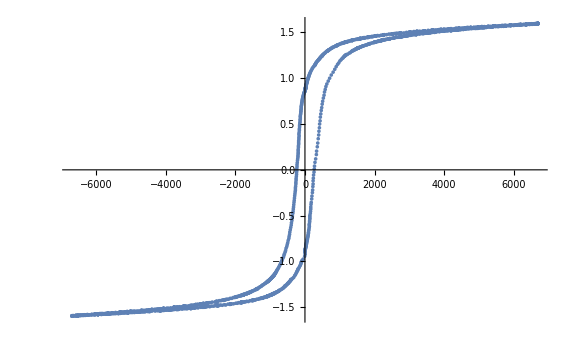

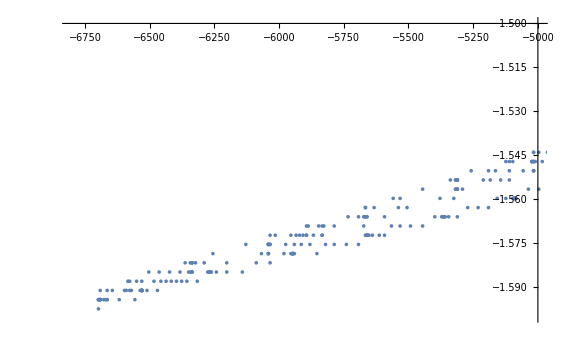

```mathematica
ListPlot[dataShifted[[1;;1950]]]
ListPlot[dataShifted[[1;;1950]],PlotRange->{{-6800,-5000},{-1.6,-1.5}}]
```

```mathematica
dataCut=dataShifted[[1;;1950]];
```

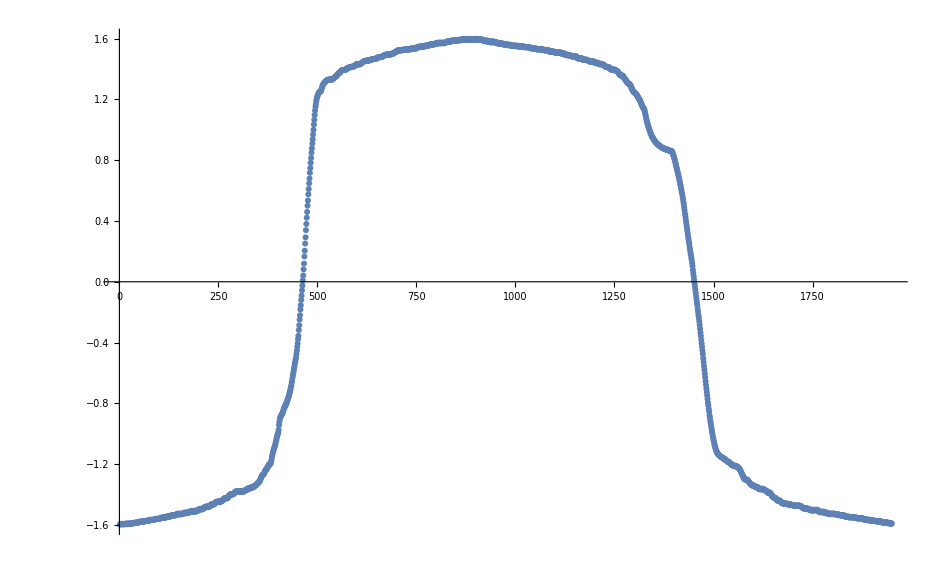

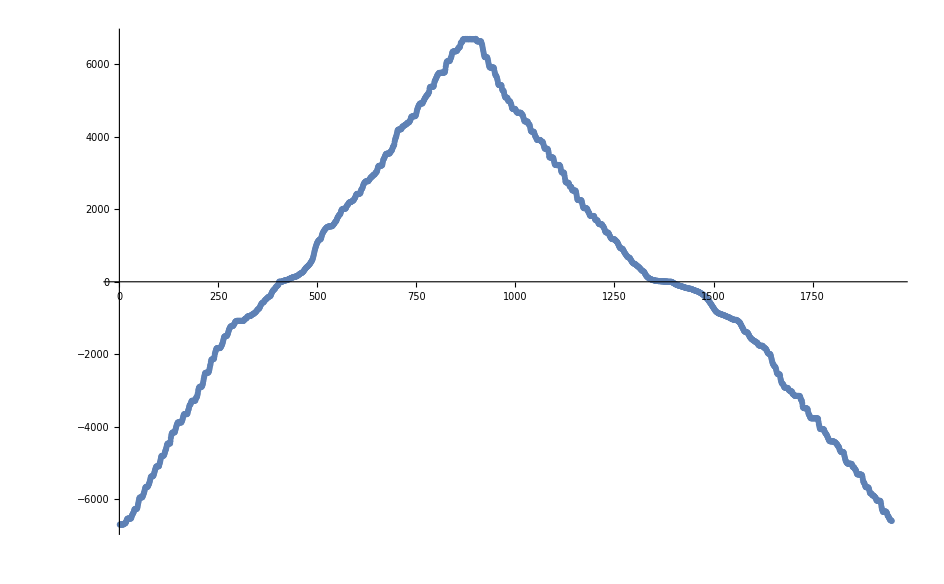

```mathematica
ListPlot[dataCut[[All,2]],PlotRange->All]
ListPlot[dataCut[[All,1]],PlotRange->All]
```

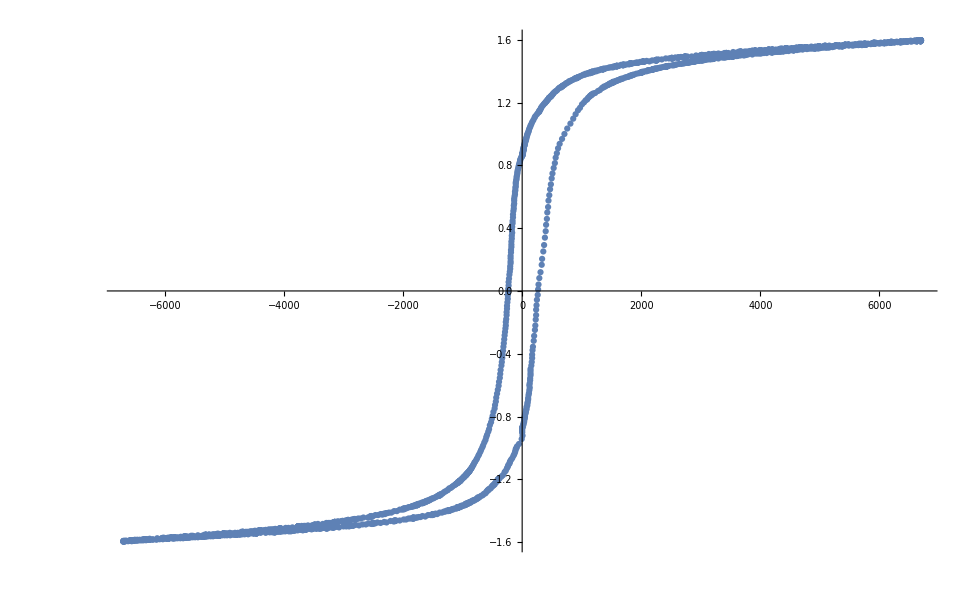

```mathematica
ListPlot[dataCut]
```

```mathematica
poly=Polygon[dataCut]
```

Polygon[…]

```mathematica
poly=Polygon[Table[dataCut[[i]],{i,1,Length[dataCut],20}]]
```

Polygon[…]

```mathematica
RegionMeasure[poly]
```

1900.43

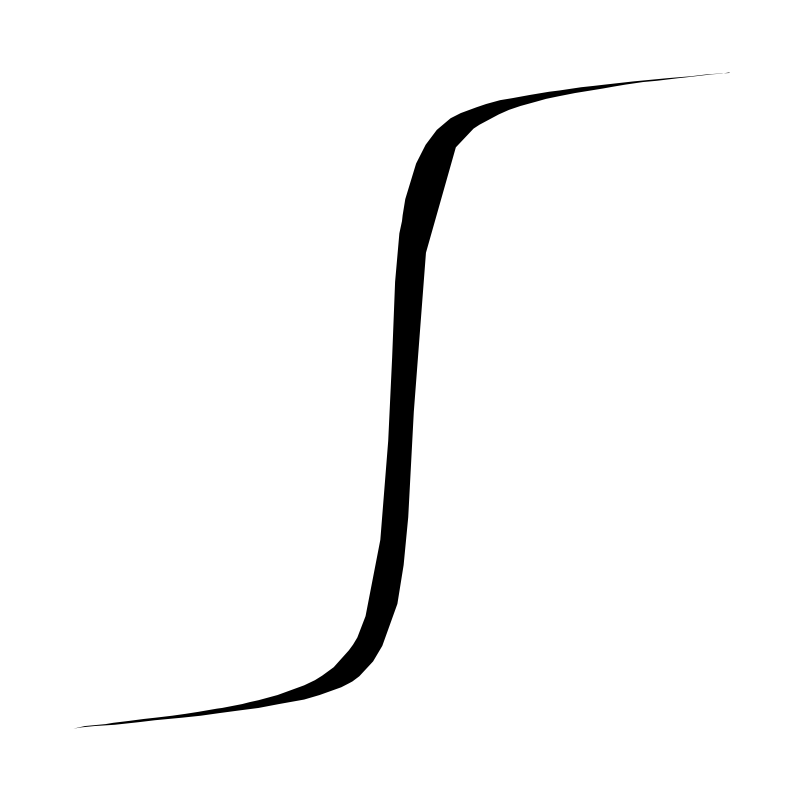

```mathematica
Graphics[poly,AspectRatio->1]
```

## Through Fitting

```mathematica
data1=dataShifted[[1;;912]];
data2=SortBy[Join[dataShifted[[912;;1950]],{dataShifted[[1]]}],First];
```

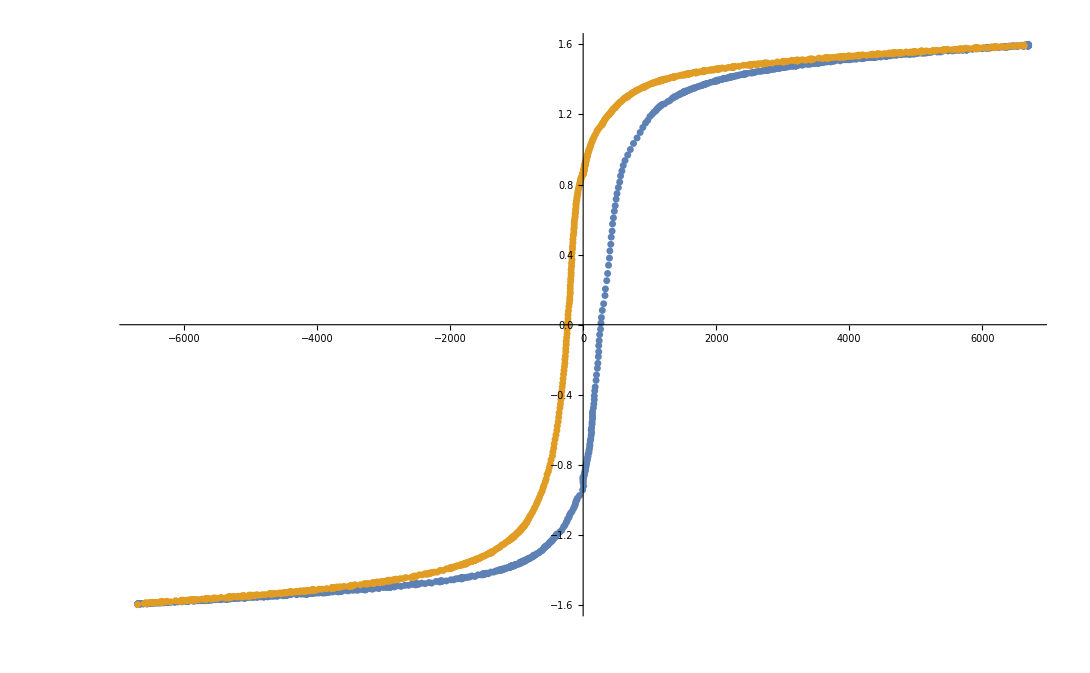

```mathematica
ListPlot[{data1,data2}]
```

```mathematica
f1=Interpolation[DeleteDuplicatesBy[data1,First],InterpolationOrder->1]
f2=Interpolation[DeleteDuplicatesBy[data2,First],InterpolationOrder->2]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
Integrate[f2[t],{t,-6700.,6630}]-Integrate[f1[t],{t,-6700.,6630}]
```

InterpolatingFunction::dmvali: The integration endpoint -6700. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

1864.15

```mathematica
1864.1466763850258/(7800)
```

0.238993

```mathematica
range=(Max[#]-Min[#]&)[dataShifted[[All,2]]]
```

3.19497

```mathematica
dHbest=19.1626419395225;
```

```mathematica
2*range*dHbest
```

122.448

```mathematica
122.44807679594257/(7800)
```

0.0156985